## Data Fitting and Exporting Figures & Parameter Tables

### Load Data

```mathematica
fileName="Data_duct_TT-Shaker.csv";
shakerData=Import[NotebookDirectory[]<>fileName];
fitData[s1_,s2_]:=Module[
{u,v,w},
u=Select[shakerData,(#⟦3⟧==s1&&#⟦7⟧==s2)&];
v=u⟦All,10⟧;
w=u⟦All,9⟧;
{ToExpression[StringDelete[w⟦#⟧,"W"]],v⟦#⟧}&/@Range[1,Min[Length[v],Length[w]],1]
];
```

### Fitting Module

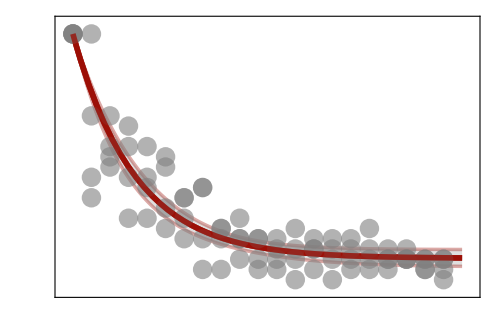

```mathematica
allDFitting[dataStrings_,freq_,color_]:=Module[
{
N0,M,p1,p2,data,NLM,fitParaters,bands,
modelPlot,bandsPlot,dataPlot,
norm,plotT,yTicks
},
N0=24;
M=6;

data=fitData[dataStrings⟦1⟧,dataStrings⟦2⟧];
NLM=NonlinearModelFit[
data,{(N0 ((-1+(1-p1)^M) ((1-p1)^M-p2)^t-p2))/(-1+(1-p1)^M-p2),0<p1<1,0<p2<1},{p1,p2},t
,Method->{"NMinimize",Method->"RandomSearch"}
];
fitParaters=Join[Quiet[NLM["ParameterTableEntries"]],Quiet[NLM["ParameterConfidenceIntervals"]],{NLM["RSquared"]}];

norm=If[freq==True,N0,1];
plotT=21;
yTicks=If[
freq==False,Join[{#/norm,ToString[#/norm]}&/@Range[0,24,4],{#/norm,""}&/@Range[2,22,4]]
,
Automatic
];
modelPlot=Plot[
NLM[t]/norm,{t,0,plotT}
,PlotRange->{plotT{-0.025,1.025},N0/norm{-0.05,1.05}}
,PlotStyle->{Thickness[0.008],Opacity[0.75,color]}
,ImageSize-> 500
,AspectRatio->0.65
,Frame->{{True,False},{True,False}}
,FrameLabel->{"",""}(*{"Cycle",If[freq==True,"Fraction in duct","Density in duct"]}*)
,FrameStyle->Directive[Thickness[0.005],Black]
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
(*,PlotLabel->"p = "<>ToString[MannWhitneyTest[{BLData⟦All,8⟧,D28Data⟦All,8⟧}]]*)
(*,PlotLegends->Placed[{"Model fit (singles)"},{0.7,0.8}]*)
(*,FrameTicks->{{yTicks,None},{All,None}}*)
,Axes->False
,FrameTicks->{{#,""}&/@Range[0,plotT,5],{#,""}&/@Range[0,1,0.2]}
];
dataPlot=ListPlot[
{data⟦#,1⟧,data⟦#,2⟧/norm}&/@Range[1,Length[data],1]
,PlotMarkers->{Automatic,20}
,PlotStyle->Opacity[0.6,Gray]
];

bands=Quiet[NLM["MeanPredictionBands",ConfidenceLevel->0.95]];

bandsPlot=ListPlot[
{{#,bands⟦1⟧/norm/.t->#}&/@Range[0,plotT,0.01],{#,bands⟦2⟧/norm/.t->#}&/@Range[0,plotT,0.01]}
,Joined->True
,Mesh->False
,PlotStyle->{{Thickness[0.005],Opacity[0.35,color]},{Thickness[0.005],Opacity[0.35,color]}}
,Filling->{1->{2}}
,FillingStyle->Opacity[0.25,Gray]
];
{fitParaters,Show[modelPlot,bandsPlot,modelPlot,dataPlot,modelPlot]}
]
fits={allDFitting[{"singles","duct"},True,ColorData["SolarColors"][0.1]],
allDFitting[{"doublets","duct"},True,ColorData["SolarColors"][0.7]],
allDFitting[{"triplets","duct"},True,ColorData["BlueGreenYellow"][0.8]],
allDFitting[{"quartets","duct"},True,ColorData["BlueGreenYellow"][0.2]]
};
fits⟦1,2⟧
```

#### Export Graphics of the fits

```mathematica
Export[NotebookDirectory[]<>"modelFit"<>ToString[#]<>"_freq.pdf",fits⟦#,2⟧,"PDF"]&/@Range[1,4,1];
```

#### Export Parameter Table

```mathematica
colNames={"parameter","best fit value","P-val. (two-sided t-test)","95% CI"};
parNames={"p1","p2"};
expNames={"1-bead","2-bead","3-bead","4-bead"};

r[x_]:=Module[
{a,o},
a=Round[x,0.0001];
o=If[a>0,a,"<0.0001"]
];
(*fits⟦1,1⟧*)
parameters=Join[
{{colNames}},
{
Join[{parNames⟦1⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦1,1⟧],r[fits⟦#,1⟧⟦1,4⟧],"["<>ToString[r[fits⟦#,1⟧⟦3,1⟧]]<>","<>ToString[r[fits⟦#,1⟧⟦3,2⟧]]<>"]"}],
Join[{parNames⟦2⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦2,1⟧],r[fits⟦#,1⟧⟦2,4⟧],"["<>ToString[r[fits⟦#,1⟧⟦4,1⟧]]<>","<>ToString[r[fits⟦#,1⟧⟦4,2⟧]]<>"]"}]
}&/@Range[1,4,1]
];
Flatten[parameters,1]⟦1⟧
Flatten[parameters,1]⟦2⟧

Export[NotebookDirectory[]<>"KineticParameters_duct.dat",Flatten[parameters,1]];
```

{parameter,best fit value,P-val. (two-sided t-test),95% CI}

{p1(1-bead),0.0439,<0.0001,[0.0379,0.0499]}

### Plot fit-Parameter Values

```mathematica
colors={ColorData["SolarColors"][0.1],ColorData["SolarColors"][0.7],ColorData["BlueGreenYellow"][0.8],ColorData["BlueGreenYellow"][0.2]}
```

{RGBColor[0.6100968, 0.04889, 0.01107652],RGBColor[0.9939926, 0.5927593999999999, 0.07059433999999999],RGBColor[0.5234324, 0.8244344, 0.4214008],RGBColor[0.0867346, 0.32334240000000003, 0.5177146]}

{{{0.0438934,0.0224612}},{{0.0255666,0.0230181}},{{0.0212813,0.0610126}},{{0.0122213,0.0874891}}}

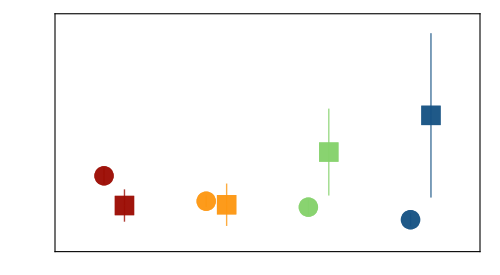

```mathematica
fittedProbabilities=Table[{
{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}(*&/@Range[1,2,1]*)
}
,{k,1,4}]

plotParameter[k_,PLflag_]:=ListPlot[
{
{{k-0.1,Around[fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦1,1⟧-fits⟦k,1⟧⟦3⟧]}}(*&/@Range[1,2,1]*),
{{k+0.1,Around[fits⟦k,1⟧⟦2,1⟧,fits⟦k,1⟧⟦2,1⟧-fits⟦k,1⟧⟦4⟧]}}(*&/@Range[1,2,1]*)
}
,PlotRange->{{0.5,4.5},0.15{-0.05,1.05}}
,PlotStyle->{
Opacity[0.8,colors⟦k⟧],
Opacity[0.8,colors⟦k⟧]
}
,PlotLegends->If[PLflag==True,Placed[{"            ","           "},Above],None]
,PlotMarkers->{Automatic,20}
,ImageSize-> 500
,AspectRatio->0.55
,Frame->{{True,False},{True,False}}
,FrameLabel->{None,None}
,FrameStyle->Directive[Thickness[0.005],Black]
(*,FrameTicks->{{{1,"1 cell"},{2,"2 cells"},{3,"3 cells"},{4,"4 cells"}},All}*)
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
(*,PlotLabel->"p = "<>ToString[MannWhitneyTest[{BLData⟦All,8⟧,D28Data⟦All,8⟧}]]*)
,FrameTicks->{{#,""}&/@Range[1,4,1],{#,""}&/@Range[0,0.16,0.05]}
]

exp=Show[plotParameter[1,True],plotParameter[2,False],plotParameter[3,False],plotParameter[4,False]]

Export[NotebookDirectory[]<>"paramterCI.pdf",exp,"PDF"];
```

### Plot Equilibrium Distributions NEW

```mathematica
M=6;
xD[{p1_,p2_}]:=p2/(p2-(1-p1)^M+1);

parameters=Join[
{{colNames}},
{
Join[{parNames⟦1⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦1,1⟧],r[fits⟦#,1⟧⟦1,4⟧],{r[fits⟦#,1⟧⟦3,1⟧],r[fits⟦#,1⟧⟦3,2⟧]}}],
Join[{parNames⟦2⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦2,1⟧],r[fits⟦#,1⟧⟦2,4⟧],{r[fits⟦#,1⟧⟦4,1⟧],r[fits⟦#,1⟧⟦4,2⟧]}}]
}&/@Range[1,4,1]
];
fittedProbabilities=Flatten[Table[{
{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}(*&/@Range[1,2,1]*)
}
,{k,1,4}],1];

Print["p_in best fits:"]
p1Fitted=fittedProbabilities⟦All,1⟧
Print["p_out best fits:"]
p2Fitted=fittedProbabilities⟦All,2⟧

Print["x_D best fits:"]
xD[{p1Fitted⟦#⟧,p2Fitted⟦#⟧}]&/@Range[1,4,1]
Print["x_L best fits:"]
(1-xD[{p1Fitted⟦#⟧,p2Fitted⟦#⟧}])&/@Range[1,4,1]

Print["95CIs for p_in:"]
p1CIs=Flatten[parameters,1]⟦#,4⟧&/@{2,4,6,8}
Print["95CIs for p_out:"]
p2sCIs=Flatten[parameters,1]⟦#+1,4⟧&/@{2,4,6,8}

Print["95CIs for x_D:"]
xDCI={
xD[{p1Fitted⟦#⟧,p2Fitted⟦#⟧}]
,{Min[Flatten[Table[xD[{p1CIs⟦#,i⟧,p2sCIs⟦#,j⟧}],{i,1,2,1},{j,1,2,1}]]],Max[Flatten[Table[xD[{p1CIs⟦#,i⟧,p2sCIs⟦#,j⟧}],{i,1,2,1},{j,1,2,1}]]]}
}&/@{1,2,3,4}

Print["95CIs for x_L:"]
xLCI={
1-xD[{p1Fitted⟦#⟧,p2Fitted⟦#⟧}]
,{Min[Flatten[Table[1-xD[{p1CIs⟦#,i⟧,p2sCIs⟦#,j⟧}],{i,1,2,1},{j,1,2,1}]]],Max[Flatten[Table[1-xD[{p1CIs⟦#,i⟧,p2sCIs⟦#,j⟧}],{i,1,2,1},{j,1,2,1}]]]}
}&/@{1,2,3,4}
```

p_in best fits:

{0.0438934,0.0255666,0.0212813,0.0122213}

p_out best fits:

{0.0224612,0.0230181,0.0610126,0.0874891}

x_D best fits:

{0.0868709,0.137882,0.335056,0.551589}

x_L best fits:

{0.913129,0.862118,0.664944,0.448411}

95CIs for p_in:

{{0.0379,0.0499},{0.0214,0.0297},{0.0159,0.0267},{0.0075,0.0169}}

95CIs for p_out:

{{0.0108,0.0341},{0.0077,0.0383},{0.0297,0.0924},{0.0282,0.1468}}

95CIs for x_D:

{{0.0868709,{0.039238,0.141487}},{0.137882,{0.0444621,0.23934}},{0.335056,{0.165386,0.501936}},{0.551589,{0.22486,0.768729}}}

95CIs for x_L:

{{0.913129,{0.858513,0.960762}},{0.862118,{0.76066,0.955538}},{0.664944,{0.498064,0.834614}},{0.448411,{0.231271,0.77514}}}

```mathematica
fits⟦1,1⟧
k=1;
xDCI⟦k⟧
Around[xDCI⟦k,1⟧,xDCI⟦k,1⟧-xDCI⟦k,2⟧]
```

{{0.0438934,0.00299577,14.6518,1.30273×10^-24},{0.0224612,0.00586427,3.83019,0.000249587},{0.0379339,0.0498529},{0.0107953,0.0341271},0.916903}

{0.0868709,{0.039238,0.141487}}

0.090.050.05

#### Plot

{RGBColor[0.6100968, 0.04889, 0.01107652],RGBColor[0.9939926, 0.5927593999999999, 0.07059433999999999],RGBColor[0.5234324, 0.8244344, 0.4214008],RGBColor[0.0867346, 0.32334240000000003, 0.5177146]}

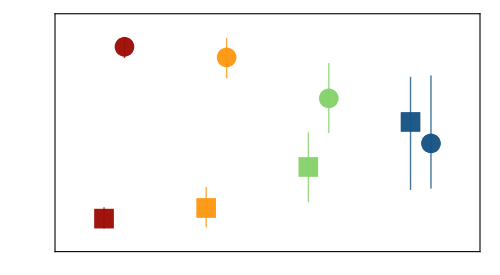

```mathematica
colors={ColorData["SolarColors"][0.1],ColorData["SolarColors"][0.7],ColorData["BlueGreenYellow"][0.8],ColorData["BlueGreenYellow"][0.2]}
equilibriumDist[k_,PLflag_]:=ListPlot[
{
{{k+0.1,Around[xLCI⟦k,1⟧,xLCI⟦k,1⟧-xLCI⟦k,2⟧]}},
{{k-0.1,Around[xDCI⟦k,1⟧,xDCI⟦k,1⟧-xDCI⟦k,2⟧]}}
}
,PlotRange->{{0.5,4.5},{-0.05,1.05}}
,PlotStyle->{
Opacity[0.8,colors⟦k⟧],
Opacity[0.8,colors⟦k⟧]
}
,PlotLegends->If[PLflag==True,Placed[{"                       ","               "},Above],None]
,PlotMarkers->{Automatic,20}
,ImageSize-> 500
,AspectRatio->0.55
,Frame->{{True,False},{True,False}}
,FrameLabel->{None,None}
,FrameStyle->Directive[Thickness[0.005],Black]
(*,FrameTicks->{{{1,"1 cell"},{2,"2 cells"},{3,"3 cells"},{4,"4 cells"}},All}*)
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
(*,PlotLabel->"p = "<>ToString[MannWhitneyTest[{BLData⟦All,8⟧,D28Data⟦All,8⟧}]]*)
,FrameTicks->{{#,""}&/@Range[1,4,1],{#,""}&/@Range[0,1,0.2]}
]

Show[equilibriumDist[1,True],equilibriumDist[2,False],equilibriumDist[3,False],equilibriumDist[4,False]]
```

#### Export PDF

```mathematica
exp=Show[equilibriumDist[1,True],equilibriumDist[2,False],equilibriumDist[3,False],equilibriumDist[4,False]];

Export[NotebookDirectory[]<>"equilibriumDist.pdf",exp,"PDF"];
```

#### Equilibrium Fraction in D with CI

```mathematica
α[{p1_,p2_}]:=(1-(1-p1)^M)/p2;


colNames={"parameter","best fit value","P-val. (two-sided t-test)","95% CI"};
parNames={"p1","p2"};
expNames={"1-bead","2-bead","3-bead","4-bead"};

r[x_]:=Module[
{a,o},
a=Round[x,0.0001];
o=If[a>0,a,"<0.0001"]
];
(*fits⟦1,1⟧*)
parameters=Join[
{{colNames}},
{
Join[{parNames⟦1⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦1,1⟧],r[fits⟦#,1⟧⟦1,4⟧],{r[fits⟦#,1⟧⟦3,1⟧],r[fits⟦#,1⟧⟦3,2⟧]}}],
Join[{parNames⟦2⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦2,1⟧],r[fits⟦#,1⟧⟦2,4⟧],{r[fits⟦#,1⟧⟦4,1⟧],r[fits⟦#,1⟧⟦4,2⟧]}}]
}&/@Range[1,4,1]
];

p=Flatten[Drop[parameters,1],1]
probs={p⟦#,2⟧,p⟦2#,2⟧}&/@Range[1,4]
probCIs={p⟦#,4⟧,p⟦2#,4⟧}&/@Range[1,4]

{probs⟦#⟧,probCIs⟦#⟧}&/@{1}

xD[{p1_,p2_}]:=1/(1+(1-(1-p1)^M)/p2)

xD[probs⟦4⟧]
```

{{p1(1-bead),0.0439,<0.0001,{0.0379,0.0499}},{p2(1-bead),0.0225,0.0002,{0.0108,0.0341}},{p1(2-bead),0.0256,<0.0001,{0.0214,0.0297}},{p2(2-bead),0.023,0.0036,{0.0077,0.0383}},{p1(3-bead),0.0213,<0.0001,{0.0159,0.0267}},{p2(3-bead),0.061,0.0002,{0.0297,0.0924}},{p1(4-bead),0.0122,<0.0001,{0.0075,0.0169}},{p2(4-bead),0.0875,0.0043,{0.0282,0.1468}}}

{{0.0439,0.0225},{0.0225,0.023},{0.0256,0.061},{0.023,0.0875}}

{{{0.0379,0.0499},{0.0108,0.0341}},{{0.0108,0.0341},{0.0077,0.0383}},{{0.0214,0.0297},{0.0297,0.0924}},{{0.0077,0.0383},{0.0282,0.1468}}}

{{{0.0439,0.0225},{{0.0379,0.0499},{0.0108,0.0341}}}}

0.401737

### Plot Equilibrium Distributions OLD

{RGBColor[0.6100968, 0.04889, 0.01107652],RGBColor[0.9939926, 0.5927593999999999, 0.07059433999999999],RGBColor[0.5234324, 0.8244344, 0.4214008],RGBColor[0.0867346, 0.32334240000000003, 0.5177146]}

{0.0438934,0.0224612}

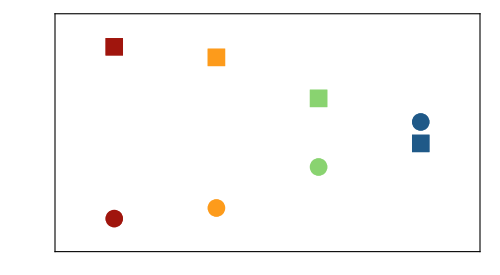

```mathematica
M=6;
colors={ColorData["SolarColors"][0.1],ColorData["SolarColors"][0.7],ColorData["BlueGreenYellow"][0.8],ColorData["BlueGreenYellow"][0.2]}
α[{p1_,p2_}]:=(1-(1-p1)^M)/p2;
{fits⟦1,1⟧⟦1,1⟧,fits⟦1,1⟧⟦2,1⟧}

equilibria[k_,PLflag_]:=ListPlot[
{{{k,(1-α[{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}]/(1+α[{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}]))}},
{{k,(α[{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}]/(1+α[{fits⟦k,1⟧⟦1,1⟧,fits⟦k,1⟧⟦2,1⟧}]))}}}
,PlotRange->{{0.5,4.5},{-0.05,1.05}}
,PlotStyle->{
Opacity[0.8,colors⟦k⟧],
Opacity[0.8,colors⟦k⟧]
}
,PlotLegends->If[PLflag==True,Placed[{"           ","           "},Above],None]
,PlotMarkers->{Automatic,18}
,ImageSize-> 500
,AspectRatio->0.55
,Frame->{{True,False},{True,False}}
,FrameLabel->{None,(*"Equilibrium distribution"*)None}
,FrameStyle->Directive[Thickness[0.005],Black]
(*,FrameTicks->{{{1,"1 cell"},{2,"2 cells"},{3,"3 cells"},{4,"4 cells"}},All}*)
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
(*,PlotLabel->"p = "<>ToString[MannWhitneyTest[{BLData⟦All,8⟧,D28Data⟦All,8⟧}]]*)
,FrameTicks->{{#,""}&/@Range[1,4,1],{#,""}&/@Range[0,1,0.2]}
]

exp=Show[equilibria[1,True],equilibria[2,False],equilibria[3,False],equilibria[4,False]]

Export[NotebookDirectory[]<>"equilibriumDist.pdf",exp,"PDF"];
```

#### Equilibrium Fraction in D with CI

```mathematica
α[{p1_,p2_}]:=(1-(1-p1)^M)/p2;


colNames={"parameter","best fit value","P-val. (two-sided t-test)","95% CI"};
parNames={"p1","p2"};
expNames={"1-bead","2-bead","3-bead","4-bead"};

r[x_]:=Module[
{a,o},
a=Round[x,0.0001];
o=If[a>0,a,"<0.0001"]
];
(*fits⟦1,1⟧*)
parameters=Join[
{{colNames}},
{
Join[{parNames⟦1⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦1,1⟧],r[fits⟦#,1⟧⟦1,4⟧],{r[fits⟦#,1⟧⟦3,1⟧],r[fits⟦#,1⟧⟦3,2⟧]}}],
Join[{parNames⟦2⟧<>"("<>ToString[expNames⟦#⟧]<>")"},
{r[fits⟦#,1⟧⟦2,1⟧],r[fits⟦#,1⟧⟦2,4⟧],{r[fits⟦#,1⟧⟦4,1⟧],r[fits⟦#,1⟧⟦4,2⟧]}}]
}&/@Range[1,4,1]
];

p=Flatten[Drop[parameters,1],1]
probs={p⟦#,2⟧,p⟦2#,2⟧}&/@Range[1,4]
probCIs={p⟦#,4⟧,p⟦2#,4⟧}&/@Range[1,4]

{probs⟦#⟧,probCIs⟦#⟧}&/@{1}

xD[{p1_,p2_}]:=1/(1+(1-(1-p1)^M)/p2)

xD[probs⟦4⟧]
```

{{p1(1-bead),0.0439,<0.0001,{0.0379,0.0499}},{p2(1-bead),0.0225,0.0002,{0.0108,0.0341}},{p1(2-bead),0.0256,<0.0001,{0.0214,0.0297}},{p2(2-bead),0.023,0.0036,{0.0077,0.0383}},{p1(3-bead),0.0213,<0.0001,{0.0159,0.0267}},{p2(3-bead),0.061,0.0002,{0.0297,0.0924}},{p1(4-bead),0.0122,<0.0001,{0.0075,0.0169}},{p2(4-bead),0.0875,0.0043,{0.0282,0.1468}}}

{{0.0439,0.0225},{0.0225,0.023},{0.0256,0.061},{0.023,0.0875}}

{{{0.0379,0.0499},{0.0108,0.0341}},{{0.0108,0.0341},{0.0077,0.0383}},{{0.0214,0.0297},{0.0297,0.0924}},{{0.0077,0.0383},{0.0282,0.1468}}}

{{{0.0439,0.0225},{{0.0379,0.0499},{0.0108,0.0341}}}}

0.401737